## Диссипация пропорциональна производной

```mathematica
f1=Pi*γ*((1-u^2)^(3/2))/(2*G)-α*u*(1-u^2)
```

-u (1-u^2) α+(π (1-u^2)^(3/2) γ)/(2 G)

```mathematica
df1du=D[f1,u]
```

2 u^2 α-(1-u^2) α-(3 π u √(1-u^2) γ)/(2 G)

```mathematica
u01=Last[Solve[f1==0,u]]
```

{u→(π γ)/(√(4 G^2 α^2+π^2 γ^2))}

```mathematica
cond1=df1du/.u01
```

(2 π^2 α γ^2)/(4 G^2 α^2+π^2 γ^2)-(3 π^2 γ^2 √(1-(π^2 γ^2)/(4 G^2 α^2+π^2 γ^2)))/(2 G √(4 G^2 α^2+π^2 γ^2))-α (1-(π^2 γ^2)/(4 G^2 α^2+π^2 γ^2))

```mathematica
Simplify[cond1]
```

-(3 π^2 γ^2 √((G^2 α^2)/(4 G^2 α^2+π^2 γ^2)))/(G √(4 G^2 α^2+π^2 γ^2))+α (-1+(3 π^2 γ^2)/(4 G^2 α^2+π^2 γ^2))

```mathematica
Reduce[Simplify[cond1]<0]
```

γ∈Reals&&((α<0&&G>0&&(γ<-(2 √(G^2 α^2))/(√5 π)||γ>(2 √(G^2 α^2))/(√5 π)))||(α>0&&((G<0&&-(2 √(G^2 α^2))/(√5 π)<γ<(2 √(G^2 α^2))/(√5 π))||G>0)))

## Диссипация пропорциональна производной*abs (производной)

```mathematica
f2=Pi*γ*((1-u^2)^(3/2))/(2*G)-2*α*u*(1-u^2)^(1/2)*F/G
```

-(2 F u √(1-u^2) α)/G+(π (1-u^2)^(3/2) γ)/(2 G)

```mathematica
df2du=D[f2,u]
```

(2 F u^2 α)/(G √(1-u^2))-(2 F √(1-u^2) α)/G-(3 π u √(1-u^2) γ)/(2 G)

```mathematica
u02=Last[Solve[f2==0,u]]
```

{u→(-2 F α+√(4 F^2 α^2+π^2 γ^2))/(π γ)}

```mathematica
cond2=df2du/.u02
```

(2 F α (-2 F α+√(4 F^2 α^2+π^2 γ^2))^2)/(G π^2 γ^2 √(1-((-2 F α+√(4 F^2 α^2+π^2 γ^2))^2)/(π^2 γ^2)))-(2 F α √(1-((-2 F α+√(4 F^2 α^2+π^2 γ^2))^2)/(π^2 γ^2)))/G-(3 (-2 F α+√(4 F^2 α^2+π^2 γ^2)) √(1-((-2 F α+√(4 F^2 α^2+π^2 γ^2))^2)/(π^2 γ^2)))/(2 G)

```mathematica
Reduce[Simplify[cond2]<0]
```

γ∈Reals&&γ≠0&&((F<0&&G>0&&α<0)||(F>0&&G>0&&α>0))

## Анализ критической скорости прохождения закоротки

```mathematica
Ekin=4*G*(1/(√(1-u^2))-1)
```

4 G (-1+1/(√(1-u^2)))

```mathematica
Epot=2*μ*√(1+2*b^2)-2*μ
```

-2 μ+2 √(1+2 b^2) μ

```mathematica
Simplify[Solve[(Ekin==Epot)/.u01,γ]]
```

{{γ→-(√2 √(α^2 μ (2 (-1+√(1+2 b^2)) G+(1+b^2-√(1+2 b^2)) μ)))/π},{γ→(√2 √(α^2 μ (2 (-1+√(1+2 b^2)) G+(1+b^2-√(1+2 b^2)) μ)))/π}}

```mathematica
G[b_]:=NIntegrate[Sqrt[(Sqrt[1+b^2*(1+Cos[x])]-1)],{x,0,Pi}]//Quiet;
```

```mathematica
J0[a_,m_]:=(√(a^2 m (8+m)))/π
```

```mathematica
J[a_,m_,b_]:=(√2 √(a^2 m (2 (-1+√(1+2 b^2)) G[b]+(1+b^2-√(1+2 b^2)) m)))/π
```

```mathematica
list=Table[{a,J[a,1,5]},{a,0,1,0.01}];
list0=Table[{m,J0[0.1,m]},{m,0,1,0.01}];
```

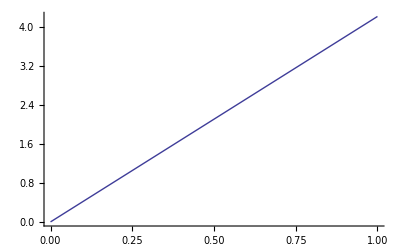

```mathematica
ListPlot[{list},Joined->True]
```

```mathematica
J[0.1,1,0.01]
```

318.469

```mathematica
J0[0.1,1]
```

0.095493

```mathematica
G[0.1]
```

1.99669

```mathematica
Sqrt[Sqrt[1+b^2*(1+Cos[x])]-1]
```

```mathematica
G[b_]:=NIntegrate[Sqrt[b*Sqrt[b^2+(1+Cos[x])]-b^2],{x,0,Pi}]//Quiet;
```

```mathematica
G[10]
```

1.99669

```mathematica
Integrate[Sqrt[(1+Cos[x])/2],{x,0,Pi}]
```

2

```mathematica
NIntegrate[Sqrt[Sqrt[100^2+(1+Cos[x])]-100],{x,0,Pi}]
```

0.199997

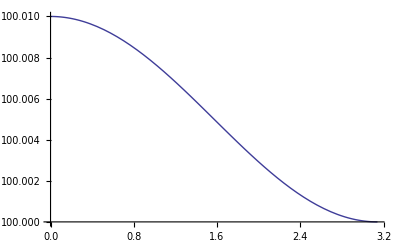

```mathematica
Plot[Sqrt[100^2+(1+Cos[x])],{x,0,Pi}]
```

```mathematica
Sqrt[100^2+2.]
```

100.01

```mathematica
100+2/2
```

101

```mathematica
Series[1+b^2-√(1+2 b^2),{b,0,4}]
```

b^4/2+O[b]^5

```mathematica
Series[(√2 √(α^2 μ (2 b (-1+√(1+2 b^2)) G+μ+b^2 μ-√(1+2 b^2) μ)))/(b π),{b,0,3}]
```

(2 √(G α^2 μ) √b)/π+(μ √(G α^2 μ) b^(3/2))/(4 G π)+(√(G α^2 μ) (-1/2-μ^2/(64 G^2)) b^(5/2))/π+O[b]^(7/2)